{0.,0.00234983,0.00469966,0.00704949,0.00939932,0.0117492,0.014099,0.0164488,0.0187986,0.0211485,0.0234983}

0.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Set::write: Tag Times in {{-0.08,-0.123875},{-0.079204,-0.125695},{-0.078408,-0.127233},{-0.0776119,-0.128478},{-0.0768159,-0.129421},{-0.0760199,-0.130053},{-0.0752239,-0.130365},{-0.0744279,-0.130348},{-0.0736318,-0.129993},{-0.0728358,-0.129295},«192»} {{-0.08,0.},{-0.079204,0.},{-0.078408,0.},{-0.0776119,0.},«3»,{-0.0744279,0.},{-0.0736318,0.},{-0.0728358,0.},«192»} is Protected.

0.00234983

Set::write: Tag Times in {{-0.08,-0.123875},{-0.079204,-0.125695},{-0.078408,-0.127233},{-0.0776119,-0.128478},{-0.0768159,-0.129421},{-0.0760199,-0.130053},{-0.0752239,-0.130365},{-0.0744279,-0.130348},{-0.0736318,-0.129993},{-0.0728358,-0.129295},«192»} {{-0.08,6.90805×10^-8},{-0.079204,8.16243×10^-8},{-0.078408,9.64453×10^-8},«6»,{-0.0728358,3.10044×10^-7},«192»} is Protected.

0.00469966

Set::write: Tag Times in {{-0.08,-0.123875},{-0.079204,-0.125695},{-0.078408,-0.127233},{-0.0776119,-0.128478},{-0.0768159,-0.129421},{-0.0760199,-0.130053},{-0.0752239,-0.130365},{-0.0744279,-0.130348},{-0.0736318,-0.129993},{-0.0728358,-0.129295},«192»} {{-0.08,2.5846×10^-7},{-0.079204,3.05393×10^-7},{-0.078408,3.60847×10^-7},«6»,{-0.0728358,1.16009×10^-6},«192»} is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

0.00704949

0.00939932

0.0117492

0.014099

0.0164488

0.0187986

0.0211485

0.0234983

{0.,0.000482983,0.00192159,0.00428499,0.00752246,0.0115643,0.0163232,0.0216959,0.0275651,0.0338016,0.0402669}

{0.,0.000305943,0.00122377,0.00275349,0.00489509,0.00764857,0.0110139,0.0149912,0.0195804,0.0247814,0.0305946}

{{0.,0.},{0.00234983,0.000482983},{0.00469966,0.00192159},{0.00704949,0.00428499},{0.00939932,0.00752246},{0.0117492,0.0115643},{0.014099,0.0163232},{0.0164488,0.0216959},{0.0187986,0.0275651},{0.0211485,0.0338016},{0.0234983,0.0402669}}

{{0.,0.},{0.00234983,0.000305943},{0.00469966,0.00122377},{0.00704949,0.00275349},{0.00939932,0.00489509},{0.0117492,0.00764857},{0.014099,0.0110139},{0.0164488,0.0149912},{0.0187986,0.0195804},{0.0211485,0.0247814},{0.0234983,0.0305946}}

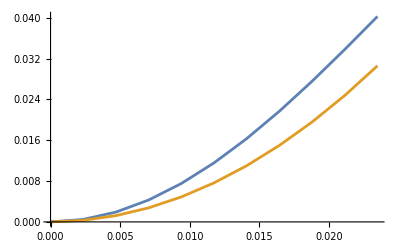

```mathematica
Eg = 1;
M = 2;
frf = 2.94383*10^9;
L = 0.04;
g = 0.04;
(*a = 0.0144687;*)
a = 0.0234983;
SF = 1;
Roffset = SF*a;

c = 299792458;

krf = 2*Pi*frf/c; 
zlims = 0.08;
zlims = If[SF<=1,zlims,L/2];
NzSteps = 201;
z = N@Subdivide[-zlims,zlims,NzSteps];
kspecial = Pi/g/2;
klower1 = If[SF<=1,0, If[kspecial<=krf,kspecial,krf]];
kupper1 = krf;
klower2 = If[SF<=1,krf,If[kspecial<=krf,krf,kspecial]];
kupper2 = 100*klower2;

Noffsets = 10;
Roffsets = N@Subdivide[0,Roffset,Noffsets]
DeltaPzStat = {};
DeltaPzTime = {};
For[i=0,i<Length[Roffsets],i++,
Roffset = Roffsets[[i+1]];
Print[Roffset];
EzJ = Eg*g/Pi*NIntegrate[Sinc[k*g/2]*BesselJ[M,√(krf^2-k^2)*Roffset]/BesselJ[M,√(krf^2-k^2)*a]*Cos[k*z],{k,klower1,kupper1}];
EzI = Eg*g/Pi*NIntegrate[Sinc[k*g/2]*BesselI[M,√(k^2-krf^2)*Roffset]/BesselI[M,√(k^2-krf^2)*a]*Cos[k*z],{k,klower2,kupper2}];
EzT = (EzJ+EzI);

TimeArray = Cos[2*Pi*frf*z/c];

dataT=Transpose@{z,EzT}
dataJ=Transpose@{z,EzJ};
  dataI=Transpose@{z,EzI};
dataTTime = Transpose@{z,EzT*TimeArray};
funStat = Interpolation[dataT]; 
AppendTo[DeltaPzStat, NIntegrate[funStat[z],{z,-zlims,zlims}]];
funTime = Interpolation[dataTTime]; 
AppendTo[DeltaPzTime, NIntegrate[funTime[z],{z,-zlims,zlims}]];
(*ListLinePlot[{dataT,dataJ,dataI}]
(*ListLinePlot[dataT]
ListLinePlot[dataJ]
ListLinePlot[dataI]*)
ListLinePlot[dataTTime]*)
]
DeltaPzStat
DeltaPzTime
dataPzStat=Transpose@{Roffsets,DeltaPzStat}
dataPzTime = Transpose@{Roffsets,DeltaPzTime}
ListLinePlot[{dataPzStat,dataPzTime}]
```

```mathematica
NumberForm[EzT,16]
```

0.7270141880969686